## Study the wobbling quantities for 136Nd

```mathematica
ClearAll["Global`*"]
```

```mathematica
ZZ=60;
AA=136;
```

### Fitting parameters

The “lower” structure has two wobbling bands (n=0,1)
The “higher” structure was three wobbling bands (n=0,1,2)

```mathematica
bandhead=10;
A1higher=0.014062276282211794;
A2higher=0.013302239436739938;
A3higher=0.012775354285838508;
A1lower=0.02295303019867904;
A2lower=0.022180318456442378;
A3lower=0.015060621351560706;
```

```mathematica
spins1higher={12,14,16,18,20,22};
spins2higher={13,15,17,19,21};
spins3higher={14,16,18,20,22,24};
energy1higher={0.39,1.051,1.895,2.894,4.055,5.321};
energy2higher={1.158,1.836,2.646,3.634,4.804};
energy3higher={1.559,2.274,3.176,4.035,4.928,5.877};
spins1lower={12,14,16};
spins2lower={11,13,15};
energy1lower={0.718,1.57,2.564};
energy2lower={0.749,1.268,2.069};
```

### Theoretical formalism

```mathematica
omega[I_,A1_,A2_,A3_]:=2I*Sqrt[(A1-A3)(A2-A3)];
En[I_,n_,A1_,A2_,A3_]:=A3*I*(I+1)+omega[I,A1,A2,A3]*(n+1/2);
Exc[I_,n_,A1_,A2_,A3_]:=En[I,n,A1,A2,A3]-En[bandhead,0,A1,A2,A3];
```

```mathematica
data1higherExp=Table[{spins1higher[[i]],energy1higher[[i]]},{i,1,Length[spins1higher]}];
data2higherExp=Table[{spins2higher[[i]],energy2higher[[i]]},{i,1,Length[spins2higher]}];
data3higherExp=Table[{spins3higher[[i]],energy3higher[[i]]},{i,1,Length[spins3higher]}];
data1higherTh=Table[{spins1higher[[i]],Exc[spins1higher[[i]],0,A1higher,A2higher,A3higher]},{i,1,Length[spins1higher]}];
data2higherTh=Table[{spins2higher[[i]],Exc[spins2higher[[i]],1,A1higher,A2higher,A3higher]},{i,1,Length[spins2higher]}];
data3higherTh=Table[{spins3higher[[i]],Exc[spins3higher[[i]],2,A1higher,A2higher,A3higher]},{i,1,Length[spins3higher]}];
data1lowerExp=Table[{spins1lower[[i]],energy1lower[[i]]},{i,1,Length[spins1lower]}];
data2lowerExp=Table[{spins2lower[[i]],energy2lower[[i]]},{i,1,Length[spins2lower]}];
data1lowerTh=Table[{spins1lower[[i]],Exc[spins1lower[[i]],0,A1lower,A2lower,A3lower]},{i,1,Length[spins1lower]}];
data2lowerTh=Table[{spins2lower[[i]],Exc[spins2lower[[i]],1,A1lower,A2lower,A3lower]},{i,1,Length[spins2lower]}];
```

### Graphical representations

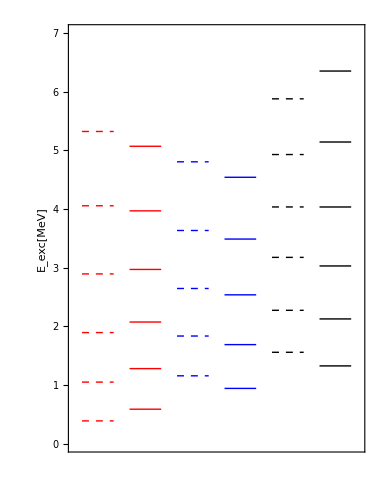

```mathematica
band1higherExp=ListLinePlot[Table[{{1,data1higherExp[[i,2]]},{3,data1higherExp[[i,2]]}},{i,1,Length[data1higherExp]}],PlotStyle->Directive[Red,Dashed,Thick],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,Automatic},{None,None}},LabelStyle->{20,Bold,Black,FontFamily->"Times"},FrameLabel->{None,"E_exc[MeV]"},ImageSize->380];
band1higherTh=ListLinePlot[Table[{{4,data1higherTh[[i,2]]},{6,data1higherTh[[i,2]]}},{i,1,Length[data1higherTh]}],PlotStyle->Directive[Red,Thick]];
band2higherExp=ListLinePlot[Table[{{7,data2higherExp[[i,2]]},{9,data2higherExp[[i,2]]}},{i,1,Length[data2higherExp]}],PlotStyle->Directive[Blue,Dashed,Thick]];
band2higherTh=ListLinePlot[Table[{{10,data2higherTh[[i,2]]},{12,data2higherTh[[i,2]]}},{i,1,Length[data2higherTh]}],PlotStyle->Directive[Blue,Thick]];
band3higherExp=ListLinePlot[Table[{{13,data3higherExp[[i,2]]},{15,data3higherExp[[i,2]]}},{i,1,Length[data3higherExp]}],PlotStyle->Directive[Black,Dashed,Thick]];
band3higherTh=ListLinePlot[Table[{{16,data3higherTh[[i,2]]},{18,data3higherTh[[i,2]]}},{i,1,Length[data3higherTh]}],PlotStyle->Directive[Black,Thick]];
obj1=Show[{band1higherExp,band1higherTh,band2higherExp,band2higherTh,band3higherExp,band3higherTh},AspectRatio->1.3,PlotRange->{{0.5,18.5},{0,7}}];
Show[obj1]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/136Nd-excitation-higher.pdf",Show[obj1]];
```

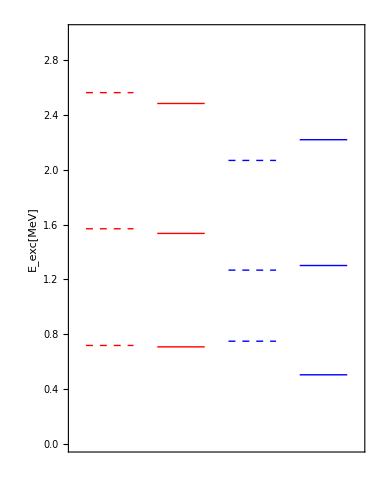

```mathematica
band1lowerExp=ListLinePlot[Table[{{1,data1lowerExp[[i,2]]},{3,data1lowerExp[[i,2]]}},{i,1,Length[data1lowerExp]}],PlotStyle->Directive[Red,Dashed,Thick],Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],FrameTicks->{{Automatic,Automatic},{None,None}},LabelStyle->{20,Bold,Black,FontFamily->"Times"},FrameLabel->{None,"E_exc[MeV]"},ImageSize->380];
band1lowerTh=ListLinePlot[Table[{{4,data1lowerTh[[i,2]]},{6,data1lowerTh[[i,2]]}},{i,1,Length[data1lowerTh]}],PlotStyle->Directive[Red,Thick]];
band2lowerExp=ListLinePlot[Table[{{7,data2lowerExp[[i,2]]},{9,data2lowerExp[[i,2]]}},{i,1,Length[data2lowerExp]}],PlotStyle->Directive[Blue,Dashed,Thick]];
band2lowerTh=ListLinePlot[Table[{{10,data2lowerTh[[i,2]]},{12,data2lowerTh[[i,2]]}},{i,1,Length[data2lowerTh]}],PlotStyle->Directive[Blue,Thick]];
obj2=Show[{band1lowerExp,band1lowerTh,band2lowerExp,band2lowerTh},AspectRatio->1.3,PlotRange->{{0.5,12.5},{0,3}}];
Show[obj2]
Export["/Users/basavyr/Documents/Work/DFT/Projects/mathematica-useful-algorithms/Physics/Wobbling-134Ce-136Nd/136Nd-excitation-lower.pdf",Show[obj2]];
```